# Einsum

## Somme di Einstein veloci per Mathematica: indici ripetuti a piacere, percorsi ottimali, diagrammi di reti tensoriali

## Caricamento

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "Kernel", "Summa.wl"}]]
```

In alternativa: PacletDirectoryLoad[cartellaEinsum]; Needs["Summa`"], oppure copia la cartella in $UserBaseDirectory/Applications.

## 1. Le basi (sintassi numpy)

```mathematica
a = RandomReal[1, {3, 4}]; b = RandomReal[1, {4, 5}]; m = RandomReal[1, {4, 4}]; u = RandomReal[1, 3]; v = RandomReal[1, 5];
```

```mathematica
Einsum["ij,jk->ik", a, b] == a . b
```

True

```mathematica
{Einsum["ii", m] == Tr[m], Einsum["ii->i", m] == Diagonal[m], Einsum["ij->ji", a] == Transpose[a]}
```

{True,True,True}

```mathematica
{Einsum["i,j->ij", u, v] == Outer[Times, u, v], Einsum["ij,jk", a, b] == a . b, Einsum["ba", a] == Transpose[a]}
```

{True,True,True}

Sintassi a liste, con etichette qualsiasi (stringhe, simboli, interi):

```mathematica
Einsum[{{"bond", "x"}, {"x", "y"}} -> {"y", "bond"}, a, b] == Transpose[a . b]
```

True

```mathematica
Einsum["αβ,βγ→αγ", a, b] == a . b
```

True

Ellissi e broadcasting, come in numpy:

```mathematica
Dimensions[Einsum["...ij,...jk->...ik", RandomReal[1, {7, 3, 4}], b]]
```

{7,3,5}

## 2. Indici ripetuti più di due volte

Ogni indice è un tensore COPY: se compare in tre o più posti è un iperarco. Nelle contrazioni intermedie diventa un indice di batch, senza bisogno di riorganizzare nulla a mano.

```mathematica
{x, y, z} = RandomReal[1, {3, 60, 70, 80}];
Einsum["ijk,ijk,ijk->", x, y, z] - Total[x y z, 3]
```

-9.67702×10^-10

```mathematica
{fa, fb, fc} = RandomReal[1, {3, 30, 6}];   (* fattori di una decomposizione CP di rango 6 *)
cp = Einsum["ai,bi,ci->abc", fa, fb, fc];
Dimensions[cp]
```

{30,30,30}

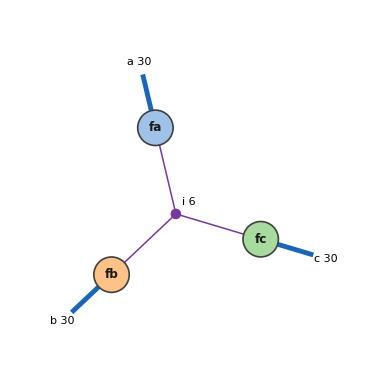

```mathematica
EinsumDiagram["ai,bi,ci->abc", fa, fb, fc]
```

```mathematica
Dimensions[Einsum["bij,bjk->bik", RandomReal[1, {10000, 3, 3}], RandomReal[1, {10000, 3, 3}]]]   (* matmul batched *)
```

{10000,3,3}

```mathematica
Einsum["iij->j", RandomReal[1, {4, 4, 3}]]   (* diagonale generalizzata + somma *)
```

{1.65175,1.60625,2.80163}

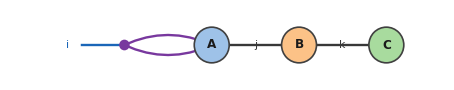

```mathematica
EinsumDiagram["iij,jk,k->i"]   (* diagonale (iperarco con gamba aperta), legami, contrazione *)
```

## 3. Un esempio fisico: norma e osservabili di un MPS

```mathematica
d = 2; chi = 32;
A1 = RandomReal[1, {d, chi}]; A2 = RandomReal[1, {chi, d, chi}]; A3 = RandomReal[1, {chi, d, chi}]; A4 = RandomReal[1, {chi, d}];
```

```mathematica
norm = Einsum["pa,aqb,brc,cs,pA,AqB,BrC,Cs->", A1, A2, A3, A4, A1, A2, A3, A4]
```

5.50769×10^7

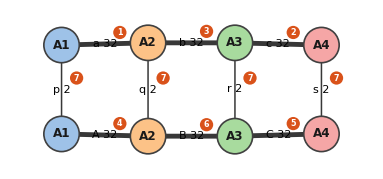

```mathematica
EinsumDiagram["pa,aqb,brc,cs,pA,AqB,BrC,Cs->", A1, A2, A3, A4, A1, A2, A3, A4, "ShowPath" -> True]
```

```mathematica
EinsumPath["pa,aqb,brc,cs,pA,AqB,BrC,Cs->", A1, A2, A3, A4, A1, A2, A3, A4]
```

<|Spec→pa,aqb,brc,cs,pA,AqB,BrC,Cs->,Path→{{1,2},{1,2},{5,6},{1,2},{1,2},{2,3},{1,2}},Method→Optimal,Contractions→{pa,aqb->pqb,brc,cs->brs,pqb,brs->pqrs,pA,AqB->pqB,BrC,Cs->Brs,pqB,Brs->pqrs,pqrs,pqrs->},StepFlops→{4096.,4096.,512.,4096.,4096.,512.,16.},Flops→17424.,NaiveFlops→1.20259×10^11,Speedup→6.90192×10^6,LargestIntermediate→128.|>

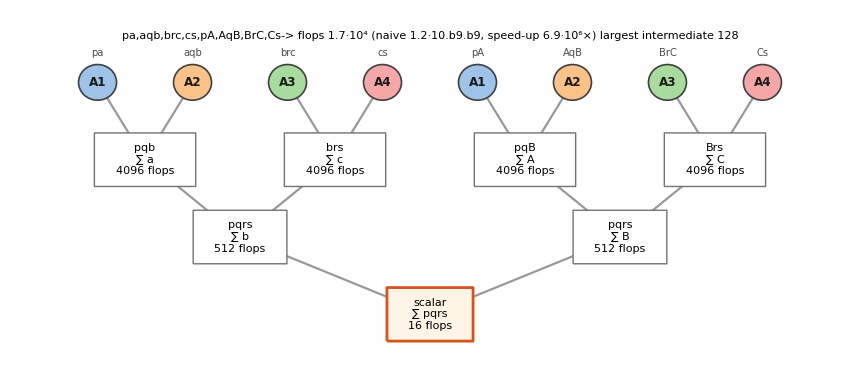

```mathematica
EinsumTree["pa,aqb,brc,cs,pA,AqB,BrC,Cs->", A1, A2, A3, A4, A1, A2, A3, A4]
```

Valore di aspettazione di σᶻ sul secondo sito:

```mathematica
sz = {{1., 0.}, {0., -1.}};
Einsum["pa,aqb,brc,cs,qQ,pA,AQB,BrC,Cs->", A1, A2, A3, A4, sz, A1, A2, A3, A4]/norm
```

0.00307573

## 4. Percorsi di contrazione

```mathematica
ma = RandomReal[1, {1000, 10}]; mb = RandomReal[1, {10, 1000}]; mc = RandomReal[1, {1000, 10}];
EinsumPath["ij,jk,kl->il", ma, mb, mc]
```

<|Spec→ij,jk,kl->il,Path→{{2,3},{1,2}},Method→Optimal,Contractions→{jk,kl->jl,ij,jl->il},StepFlops→{100000.,100000.},Flops→200000.,NaiveFlops→2.×10^8,Speedup→1000.,LargestIntermediate→10000.|>

```mathematica
Table[{p, First[RepeatedTiming[Einsum["ij,jk,kl->il", ma, mb, mc, "Path" -> p]]]}, {p, {"Optimal", "Greedy", "Sequential"}}]
```

{{Optimal,0.000134098},{Greedy,0.000138403},{Sequential,0.000525551}}

```mathematica
EinsumPath["ij,jk,kl->il", {{1000, 10}, {10, 1000}, {1000, 10}}, "Path" -> {{1, 2}, {1, 2}}]   (* percorso imposto, formato numpy *)
```

<|Spec→ij,jk,kl->il,Path→{{1,2},{1,2}},Method→User,Contractions→{ij,jk->ik,kl,ik->il},StepFlops→{1.×10^7,1.×10^7},Flops→2.×10^7,NaiveFlops→2.×10^8,Speedup→10.,LargestIntermediate→1.×10^6|>

## 5. EinsumFunction: piani precompilati per i loop

```mathematica
ef = EinsumFunction["bi,ij,bj->b", {{5000, 64}, {64, 64}, {5000, 64}}]
```

EinsumFunction[…]

```mathematica
xs = RandomReal[1, {5000, 64}]; w = RandomReal[1, {64, 64}];
{First[RepeatedTiming[ef[xs, w, xs]]], First[RepeatedTiming[Einsum["bi,ij,bj->b", xs, w, xs]]], First[RepeatedTiming[Total[(xs . w) xs, {2}]]]}
```

{0.000741962,0.000764636,0.000310712}

```mathematica
ef["Properties"]
```

{Spec,Shapes,Path,Method,Flops,NaiveFlops,Speedup,LargestIntermediate,Contractions,Diagram,Tree,Plan}

## 6. Diagrammi di reti tensoriali

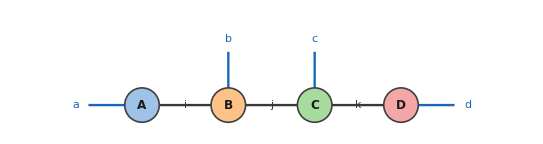

```mathematica
EinsumDiagram["ai,ibj,jck,kd->abcd"]   (* MPS *)
```

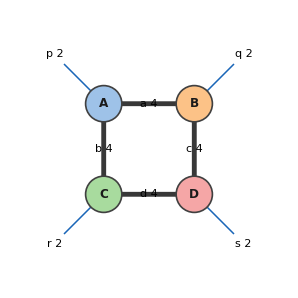

```mathematica
EinsumDiagram["pab,qac,rbd,scd->pqrs", {{2, 4, 4}, {2, 4, 4}, {2, 4, 4}, {2, 4, 4}}]   (* PEPS 2x2 *)
```

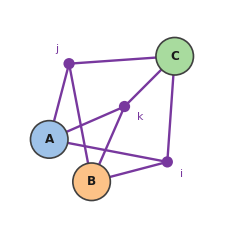

```mathematica
EinsumDiagram["ijk,ijk,ijk->"]   (* tre iperarchi *)
```

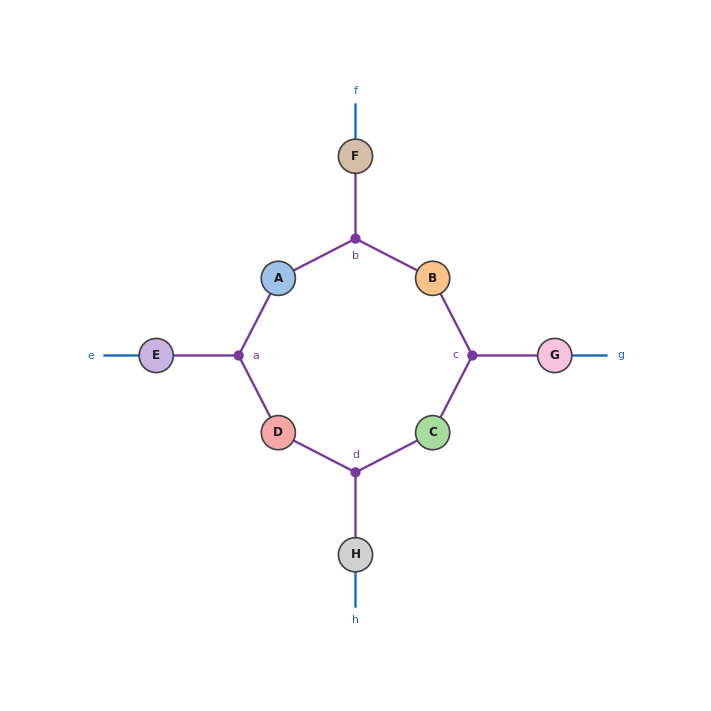

```mathematica
EinsumDiagram["ab,bc,cd,da,ae,bf,cg,dh->efgh"]   (* anello con iperarchi *)
```

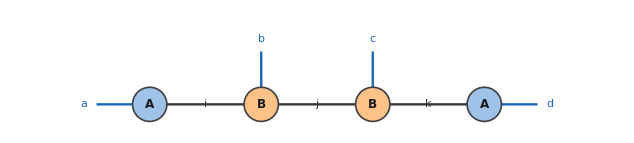

```mathematica
EinsumDiagram["ai,ibj,jck,kd->abcd", "Layout" -> "Line", "TensorNames" -> {"A", "B", "B", "A"}]
```

Una griglia L×L costruita col codice, usando la sintassi a liste (le etichette possono essere espressioni):

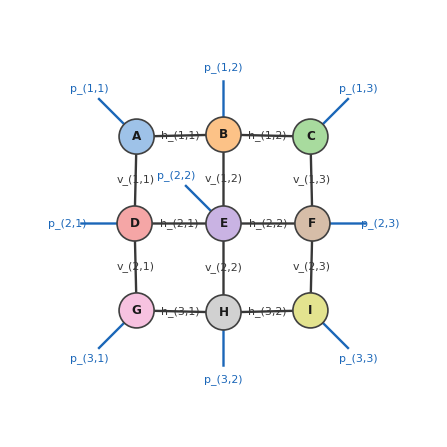

```mathematica
L = 3;
legs[i_, j_] := Join[If[j > 1, {Subscript["h", i, j - 1]}, {}], If[j < L, {Subscript["h", i, j]}, {}],
   If[i > 1, {Subscript["v", i - 1, j]}, {}], If[i < L, {Subscript["v", i, j]}, {}], {Subscript["p", i, j]}];
gridSpec = Flatten[Table[legs[i, j], {i, L}, {j, L}], 1] -> Flatten[Table[Subscript["p", i, j], {i, L}, {j, L}]];
EinsumDiagram[gridSpec, "ShowDimensions" -> False]
```

```mathematica
peps = Table[RandomReal[1, ConstantArray[2, Length[legs[i, j]]]], {i, L}, {j, L}];
Dimensions[Einsum[gridSpec, Sequence @@ Flatten[peps, 1]]]
```

{2,2,2,2,2,2,2,2,2}

La contrazione passo per passo (la coppia evidenziata è quella che verrà contratta):

```mathematica
ListAnimate[EinsumDiagram["pab,qac,rbd,scd->pqrs", {{2, 4, 4}, {2, 4, 4}, {2, 4, 4}, {2, 4, 4}}, "Steps" -> True], AnimationRunning -> False]
```

## 7. Prestazioni

Benchmark completo: Get["../Examples/Benchmarks.wl"]. Alcuni confronti rapidi:

```mathematica
{ba, bb} = RandomReal[1, {2, 20000, 4, 4}];
{First[RepeatedTiming[Einsum["bij,bjk->bik", ba, bb]]], First[RepeatedTiming[MapThread[Dot, {ba, bb}]]]}
```

{0.0241146,0.012372}

```mathematica
{t1, t2, t3} = RandomReal[1, {3, 100, 100, 100}];
{First[RepeatedTiming[Einsum["ijk,ijk,ijk->", t1, t2, t3]]], First[RepeatedTiming[Total[t1 t2 t3, 3]]]}
```

{0.00352645,0.00274084}

```mathematica
EinsumClearCache[]
```